```mathematica
(* CVIČENÍ 9 *)
(* PŘÍKLAD 5 - ZE CVIČENÍ 8 *)
```

```mathematica
-Graphics-
(* 
Pro obvod na obrázku platí u(t)=5*sin(10^4 t + 2.1), R = 1kΩ, C = 1μF.
1. Řešte obvod jak klasicky (pomocí NDSolve) metodou uzlových napětí, tak v HUS. V obou případech zobrazte napětí u2(t) v časovém intervalu 0≤t≤0.025.
2. Vykreslete přenos obvodu pro 10≤ω≤10^7 
*)
-Graphics-
```

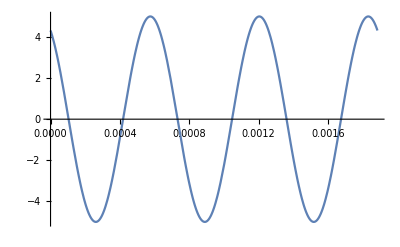

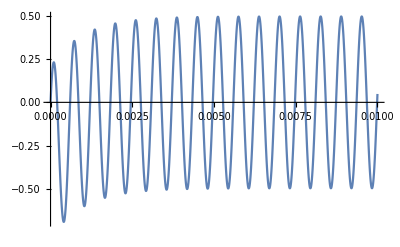

```mathematica
ClearAll["Global`*"]
(* Reseni pomoci NDSolve v casove oblasti *)
(* definice soucastek a zdroje *)
soucastky = {R1 -> 1*10^3,C1->1*10^-6};
uZ[t_]:=5*Sin[10^4*t+2.1];



Uamplituda = 5;
kruhovaFrekvence = 10^4;
frekvence = 10^4/(2*π);
fazPosuv = 2.1;
perioda = 1/frekvence;
tmax = 3*perioda;

Plot[uZ[t],{t,0,tmax}]

(* rovnice uzlu *)
uzel1 = iUz[t]+iR1[t]==0;
uzel2=iR1[t]==iC1[t];

(* rovnice soucastek *)
rez1 = iR1[t]==(u1[t]-u2[t])/R1;
kond1 = iC1[t]==C1*u2'[t];
zdroj = u1[t]==uZ[t];

(* pocatecni podminky *)
pp1 = u2[0]==0;

nezname = {u1[t],u2[t],iUz[t],iR1[t],iC1[t]};
rovnice = {uzel1,uzel2,rez1,kond1,zdroj,pp1};

reseni = NDSolve[rovnice/.soucastky,nezname,{t,0,0.025}];

Plot[u2[t]/.reseni,{t,0,0.01}]
```

-Graphics-

{{u1→-2.52423+4.31605 ⅈ,u2→(4316.05+2524.23 ⅈ)/((0.-1000. ⅈ)+1. ω),iUz→((0.00252423-0.00431605 ⅈ) ω)/((0.-1000. ⅈ)+1. ω),iR1→-((0.00252423-0.00431605 ⅈ) ω)/((0.-1000. ⅈ)+1. ω),iC1→-((0.00252423-0.00431605 ⅈ) ω)/((0.-1000. ⅈ)+1. ω)}}

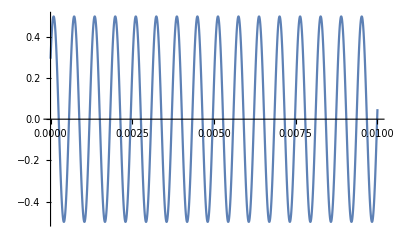

```mathematica
ClearAll["Global`*"]
(* Reseni pomoci v HUSu *)
(* definice soucastek a zdroje *)
soucastky = {R1 -> 1*10^3,C1->1*10^-6};
uZ[t_]:=5*Sin[10^4*t+2.1];

Uamplituda = 5;
kruhovaFrekvence = 10^4;
omega = {ω-> 10^4};
frekvence = 10^4/(2*π);
φ = 2.1;
perioda = 1/frekvence;
tmax = 3*perioda;

Uf = Uamplituda*ⅇ^(ⅉ*φ);

Plot[Im[Uf*ⅇ^(ⅉ*ω*t)/.omega],{t,0,tmax}]

(* rovnice uzlu *)
uzel1 = iUz+iR1==0;
uzel2=iR1==iC1;

(* rovnice soucastek *)
rez1 = iR1==(u1-u2)/R1;
kond1 = u2== iC1*1/(ⅉ*ω*C1); 
zdroj = u1==Uf;


nezname = {u1,u2,iUz,iR1,iC1};
rovnice = {uzel1,uzel2,rez1,kond1,zdroj};

reseni = Solve[rovnice/.soucastky,nezname]

Plot[Im[(u2/.reseni)*ⅇ^(ⅉ*ω*t)/.omega],{t,0,0.01}]
```

```mathematica
(* Vykresleni prenosu *)
prenos = (u2/.reseni)/Uf
```

{-(1.13687×10^-13+1000. ⅈ)/((0.-1000. ⅈ)+1. ω)}

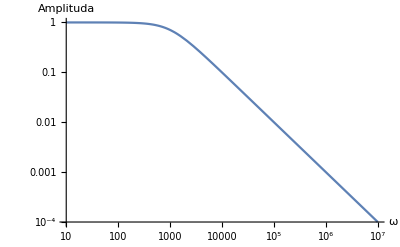

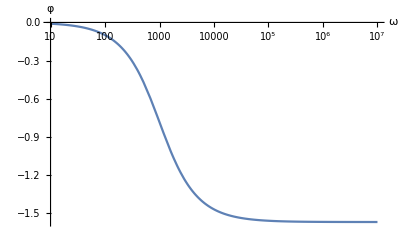

```mathematica
(* Vykresleni amplitudy zavisle na frekvenci *)
LogLogPlot[Abs[prenos],{ω,10,10^7}, AxesLabel->{"ω","Amplituda"}] (* ESC + o + ESC / ESC + w + ESC *)
(* Vykresleni fazoveho posuvu zavisleho na frekvenci *)
LogLinearPlot[Arg[prenos],{ω,10,10^7}, AxesLabel->{"ω","φ"}] (* ESC + j + ESC *)
```

```mathematica
(* Příklad 5 *)
```

```mathematica
(*
Pro obvod na obrázku platí u(t)=12.5*sin(10^5 t+1.2),R1=10kΩ, R2=10kΩ,C1=10nF.
1. Řešte obvod jak klasicky (pomocí NDSolve) metodou uzlových napětí,tak v HUS.V obou případech zobrazte napětí uout(t) v časovém intervalu 0≤t≤0.4 ms.
2.Vykreslete přenos obvodu pro 10≤ω≤10^7
*)
-Graphics-;
-Graphics-;
(*(* PŘÍKLAD 5 - řešení pomocí impedance *)
ClearAll["Global`*"]
soucastky = {R1 -> 10*10^3,R2 -> 10*10^3,C1 -> 10*10^-9};
Uf = 12.5*ⅇ^(ⅉ*1.2);
tmax = 0.4*10^-3;
ZR1 = R1;
ZR2 = R2;
ZC1 = 1/(ⅉ*ω*C1);

rovnice = {

IU +IR1==0,
IR1==IC1+IR2,

R1 == (U1-U2)/IR1,
R2 == U2/IR2,
U2==IC1*1/(ⅉ*ω*C1),
U1==Uf
};
nezname = {IU,IR1,IR2,IC1,U1,U2};
reseni = Solve[rovnice/.soucastky, nezname]*)
```

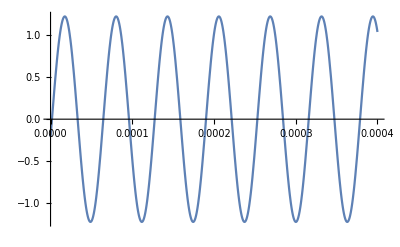

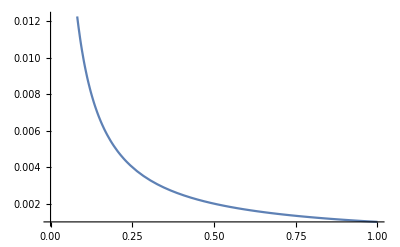

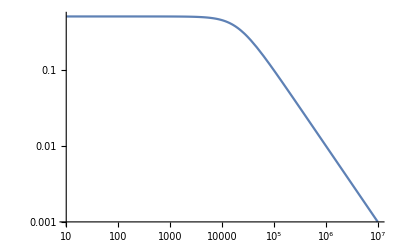

```mathematica
ClearAll["Global`*"]
(* RESENI V HUSu *)
(* definice soucastek a zdroje *)
soucastky={R1-> 10*10^3,R2-> 10*10^3,C1-> 10*10^-9};
Uamplituda = 12.5;
omega = ω ->  10^5;
φ = 1.2;
Uf=Uamplituda*ⅇ^(ⅉ*φ);

tmax1=0.4*10^-3;

Plot[Im[(Uf*ⅇ^(ⅉ*ω*t))/.omega],{t,0,tmax1}];

(* rovnice uzlu *)
uzel1 = iUz+iR1==0;
uzel2 = iR1==iC1+iR2;

(* rovnice soucastek *)
rez1 = iR1==(u1-u2)/R1;
rez2 = iR2==u2/R2;
kond1 = u2==iC1*1/(ⅉ*ω*C1);
zdroj = u1==Uf;


(* vypocet *)
nezname = {iUz,iR1,iR2,iC1,u1,u2};
rovnice = {uzel1,uzel2,rez1,rez2,kond1,zdroj};

reseni = Solve[rovnice/.soucastky,nezname];
Plot[{Im[(u2/.reseni)*ⅇ^(ⅉ*ω*t)/.omega]},{t,0,tmax1}]

(* Vykresleni prenosu *)
Plot[Abs[u2/Uf]/.reseni,{ω,10,10^7}]
LogLogPlot[Abs[u2/Uf]/.reseni,{ω,10,10^7},PlotRange->All]
```

```mathematica
(* Příklad 8 *)
```

```mathematica
-Graphics-;
ClearAll["Global`*"]
Uin = 130+15*ⅉ
Uout = 9-9.5ⅉ
Prenos = Uout/Uin
20*Log10[Abs[Uin/Uout]]
```

130+15 ⅈ

9.-9.5 ⅈ

0.06-0.08 ⅈ

20.

```mathematica
(* Příklad 9 *)
```

```mathematica
-Graphics-;
ClearAll["Global`*"]
Uin = 10+5.6*ⅉ
Ics = 0.1+0.03*ⅉ
Zcs = Uin/Ics
```

10.+5.6 ⅈ

0.1+0.03 ⅈ

107.156+23.8532 ⅈ

```mathematica
(*Příklad 7 *)
(* Impedance - napěťový dělič *)
```

```mathematica
ClearAll["Global`*"]
soucastky = {R1->10000,R2->10000, C1-> 10*10^-9,L1-> 10*10^-3};
Uin = 4.2+3.1*ⅉ;
omega = ω->2*π*1000;

ZR1 = R1;
ZR2 =R2;
ZC1 = 1/(ⅉ*ω*C1);
ZL1 = ⅉ*ω*L1;

ZR2L1 = ZR2+ZL1;
ZR1C1 = 1/(1/ZR1+1/ZC1);

Uout = Uin*ZR2L1/(ZR1C1+ZR2L1)/.soucastky/.omega

Prenos = Uout/Uin
```

1.84057+2.29706 ⅈ

0.545002+0.144657 ⅈ